## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="G3PD2";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = False; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)


(* user will need to change this path *)
pathMASSef = "/home/mrama/Dropbox/test bla/MASSef/";
kineticDataFileName =  "kinetic_data.csv";

mainFolder = "fit_G3PD2_typeII";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:/home/mrama/Dropbox/test bla/MASSef/examples/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName,  assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological];
```

(glyc3p^c+nadp^c⇌dhap^c+h^c+nadph^c)^G3PD2

ordered bi bi; [nadp,glyc3p,dhap,nadph]

Structure:

Active sites:

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | glyc3p,Null;nadp,Null | 0.000024 | 0.0000228
0.0000252 | Null | Null | 7 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | nadph | 3.4×10^-6 | 3.23×10^-6
3.57×10^-6 |  | M | 7.4 | 23 | trishcl | 0.1 | 
1 | dhap | 0.00018 | 0.000171
0.000189 |  | M | 7.4 | 23 | trishcl | 0.1 | 
1 | nadp | 0.000165 | 0.00015675
0.00017325 |  | M | 7.4 | 23 | trishcl | 0.1 | 
1 | glyc3p | 0.00003 | 0.0000285
0.0000315 |  | M | 7.4 | 23 | trishcl | 0.1 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kic | glyc3p | 4.2×10^-6 | 3.99×10^-6
4.41×10^-6 | nadph | 0.0001 | Competitive | dhap | 0.00018 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincu | glyc3p | 6.5×10^-6 | 6.175×10^-6
6.825×10^-6 | dhap | 0.0001 | NonCompetitive | nadph | 3.4×10^-6 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincc | glyc3p | 2.5×10^-6 | 2.375×10^-6
2.625×10^-6 | dhap | 0.0001 | NonCompetitive | nadph | 3.4×10^-6 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincu | nadp | 0.0013 | 0.001235
0.001365 | nadph | 0.00001 | NonCompetitive | dhap | 0.00018 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincc | nadp | 0.0013 | 0.001235
0.001365 | nadph | 0.00001 | NonCompetitive | dhap | 0.00018 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kic | nadp | 0.000187 | 0.00017765
0.00019635 | dhap | 0.002 | Competitive | nadph | 3.4×10^-6 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kic | dhap | 0.000038 | 0.0000361
0.0000399 | nadp | 0.002 | Competitive | glyc3p | 0.00003 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincu | dhap | 0.00024 | 0.000228
0.000252 | glyc3p | 0.0001 | NonCompetitive | nadp | 0.000165 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincc | dhap | 0.00012 | 0.000114
0.000126 | glyc3p | 0.0001 | NonCompetitive | nadp | 0.000165 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincu | nadph | 8.×10^-7 | 7.6×10^-7
8.4×10^-7 | nadp | 0.0001 | NonCompetitive | glyc3p | 0.00003 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincc | nadph | 6.×10^-7 | 5.7×10^-7
6.3×10^-7 | nadp | 0.0001 | NonCompetitive | glyc3p | 0.00003 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kic | nadph | 4.×10^-7 | 3.8×10^-7
4.2×10^-7 | glyc3p | 0.0002 | Competitive | nadp | 0.000165 | M | 7.4 | 23 | trishcl | 0.1 |

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority (optional)

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1,1,1,1};
s05Priorities = Null;
kcatPriorities = Null;
inhibitionPriorities={1,1,1, 1,1,1,1,1,1,1,1,1};
activationPriorities = Null;
otherParamsPriorities = Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(glyc3p^c+nadp^c⇌dhap^c+h^c+nadph^c)^G3PD2

ordered bi bi; [nadp,glyc3p,dhap,nadph]

Structure:

Active sites:

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | glyc3p,Null;nadp,Null | 0.000024 | 0.0000228
0.0000252 | Null | Null | 7 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | nadph | 3.4×10^-6 | 3.23×10^-6
3.57×10^-6 |  | M | 7.4 | 23 | trishcl | 0.1 | 
1 | dhap | 0.00018 | 0.000171
0.000189 |  | M | 7.4 | 23 | trishcl | 0.1 | 
1 | nadp | 0.000165 | 0.00015675
0.00017325 |  | M | 7.4 | 23 | trishcl | 0.1 | 
1 | glyc3p | 0.00003 | 0.0000285
0.0000315 |  | M | 7.4 | 23 | trishcl | 0.1 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kic | glyc3p | 4.2×10^-6 | 3.99×10^-6
4.41×10^-6 | nadph | 0.0001 | Competitive | dhap | 0.00018 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincu | glyc3p | 6.5×10^-6 | 6.175×10^-6
6.825×10^-6 | dhap | 0.0001 | NonCompetitive | nadph | 3.4×10^-6 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincc | glyc3p | 2.5×10^-6 | 2.375×10^-6
2.625×10^-6 | dhap | 0.0001 | NonCompetitive | nadph | 3.4×10^-6 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincu | nadp | 0.0013 | 0.001235
0.001365 | nadph | 0.00001 | NonCompetitive | dhap | 0.00018 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincc | nadp | 0.0013 | 0.001235
0.001365 | nadph | 0.00001 | NonCompetitive | dhap | 0.00018 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kic | nadp | 0.000187 | 0.00017765
0.00019635 | dhap | 0.002 | Competitive | nadph | 3.4×10^-6 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kic | dhap | 0.000038 | 0.0000361
0.0000399 | nadp | 0.002 | Competitive | glyc3p | 0.00003 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincu | dhap | 0.00024 | 0.000228
0.000252 | glyc3p | 0.0001 | NonCompetitive | nadp | 0.000165 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincc | dhap | 0.00012 | 0.000114
0.000126 | glyc3p | 0.0001 | NonCompetitive | nadp | 0.000165 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincu | nadph | 8.×10^-7 | 7.6×10^-7
8.4×10^-7 | nadp | 0.0001 | NonCompetitive | glyc3p | 0.00003 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincc | nadph | 6.×10^-7 | 5.7×10^-7
6.3×10^-7 | nadp | 0.0001 | NonCompetitive | glyc3p | 0.00003 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kic | nadph | 4.×10^-7 | 3.8×10^-7
4.2×10^-7 | glyc3p | 0.0002 | Competitive | nadp | 0.000165 | M | 7.4 | 23 | trishcl | 0.1 |

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Construct Module and Set Up Comparison Equations

### Construct enzyme module

```mathematica
catalyticBranch={"E_G3PD2[c] + nadp[c] <=> E_G3PD2[c]&nadp",
				"E_G3PD2[c]&nadp + glyc3p[c] <=> E_G3PD2[c]&nadp&glyc3p",
				"E_G3PD2[c]&nadp&glyc3p <=> E_G3PD2[c]&nadph&dhap",
				"E_G3PD2[c]&nadph&dhap <=> E_G3PD2[c]&nadph + dhap[c]",
				"E_G3PD2[c]&nadph <=> E_G3PD2[c] + nadph[c]"};


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites-> 0];
enzymeModel["Reactions"]
```

{((G3PD2^c)_^+nadp^c⇌(G3PD2^c&nadp^c)_^)^G3PD21,((G3PD2^c&nadph^c)_^⇌(G3PD2^c)_^+nadph^c)^G3PD22,((G3PD2^c&nadp^c)_^+glyc3p^c⇌(G3PD2^c&nadp^c&glyc3p^c)_^)^G3PD23,((G3PD2^c&nadph^c&dhap^c)_^⇌(G3PD2^c&nadph^c)_^+dhap^c)^G3PD24,((G3PD2^c&nadp^c&glyc3p^c)_^⇌(G3PD2^c&nadph^c&dhap^c)_^)^G3PD25}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((G3PD2^c)_^+nadp^c⇌(G3PD2^c&nadp^c)_^)^G3PD21,Overscript[(G3PD2^c&nadph^c)_^⇌(G3PD2^c)_^+nadph^c, G3PD22],((G3PD2^c&nadp^c)_^+glyc3p^c⇌(G3PD2^c&nadp^c&glyc3p^c)_^)^G3PD23,Overscript[(G3PD2^c&nadph^c&dhap^c)_^⇌(G3PD2^c&nadph^c)_^+dhap^c, G3PD24],((G3PD2^c&nadp^c&glyc3p^c)_^⇌(G3PD2^c&nadph^c&dhap^c)_^)^G3PD25};
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

### Setup King-Altman Equations

```mathematica
MWCFlag=False;
nActiveSites=1;
simplifyFlag=True;
simplifyMaxTime=300;
otherMetsReverseZeroSub={{"prod_inhib_dhap", nadph^c->0},{ "prod_inhib_nadph", dhap^c->0}};
otherMetsForwardZeroSub={{"prod_inhib_glyc3p", nadp^c->0},{"prod_inhib_nadp", glyc3p^c->0}};
inhibitionListSubset=inhibitionList[[{2,3,8,9}]];

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpFluxEquations[enzymeModel, rxn, rxnName, inputPath, inhibitionList,inhibitionListSubset, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites];
```

{glyc3p^c→0,nadp^c→0}

{dhap^c→0,nadph^c→0}

{glyc3p^c→∞,nadp^c→∞}

{dhap^c→∞,nadph^c→∞}

prod inhib

Generating flux equation...

{((G3PD2^c&nadp^c&glyc3p^c)_^-((G3PD2^c&nadph^c&dhap^c)_^)/K_G3PD25) Volume_c k_G3PD25^⟶}

Volume_c (-(G3PD2^c&nadph^c&dhap^c)_^ k_G3PD25^⟵+(G3PD2^c&nadp^c&glyc3p^c)_^ k_G3PD25^⟶)

1

2

3

0.372027

4

0.00124

5

0.00015

Simplifying...

6

0.17835

{((G3PD2^c&nadph^c)_^+glyc3p^c⇌(G3PD2^c&nadph^c&glyc3p^c)_^)^G3PD2_Kincu_glyc3p_1_nadph,((G3PD2^c)_^+glyc3p^c⇌(G3PD2^c&glyc3p^c)_^)^G3PD2_Kincc_glyc3p_1_nadph,((G3PD2^c&glyc3p^c)_^+nadph^c⇌(G3PD2^c&nadph^c&glyc3p^c)_^)^G3PD2_NC_glyc3p,((G3PD2^c&nadp^c)_^+dhap^c⇌(G3PD2^c&nadp^c&dhap^c)_^)^G3PD2_Kincu_dhap_1_nadp,((G3PD2^c)_^+dhap^c⇌(G3PD2^c&dhap^c)_^)^G3PD2_Kincc_dhap_1_nadp,((G3PD2^c&dhap^c)_^+nadp^c⇌(G3PD2^c&nadp^c&dhap^c)_^)^G3PD2_NC_dhap}

{}

{((G3PD2^c&nadp^c&glyc3p^c)_^-((G3PD2^c&nadph^c&dhap^c)_^)/K_G3PD25) Volume_c k_G3PD25^⟶}

Generating flux equation...

{((G3PD2^c&nadp^c&glyc3p^c)_^-((G3PD2^c&nadph^c&dhap^c)_^)/K_G3PD25) Volume_c k_G3PD25^⟶}

Volume_c (-(G3PD2^c&nadph^c&dhap^c)_^ k_G3PD25^⟵+(G3PD2^c&nadp^c&glyc3p^c)_^ k_G3PD25^⟶)

1

2

3

30.9247

4

0.01783

5

0.000613

Simplifying...

6

81.841142

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating other relative rate forward equation...

Simplifying...

{prod_inhib_dhap,nadph^c→0}

{glyc3p^c→∞,nadp^c→∞}

{prod_inhib_nadph,dhap^c→0}

{glyc3p^c→∞,nadp^c→∞}

Generating other relative rate reverse equation...

Simplifying...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

## Semi-Automated Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList
, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

Simulating inhibition data...

```mathematica
FilePrint@dataPathList
```

Priority	dhap[c]	glyc3p[c]	nadp[c]	nadph[c]	param_G3PD2_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/haldaneRatio_1.txt"	0.000024
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/haldaneRatio_1.txt"	0.000024
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/haldaneRatio_1.txt"	0.000024
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/haldaneRatio_1.txt"	0.000024
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/haldaneRatio_1.txt"	0.000024
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/haldaneRatio_1.txt"	0.000024
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/haldaneRatio_1.txt"	0.000024
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/haldaneRatio_1.txt"	0.000024
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/haldaneRatio_1.txt"	0.000024
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/haldaneRatio_1.txt"	0.000024
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/haldaneRatio_1.txt"	0.000024
1	0.01	0	0	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_nadph.txt"	0.09090909090909097
1	0.01	0	0	5.388636854367791e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_nadph.txt"	0.1368068886032101
1	0.01	0	0	8.540413867132584e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_nadph.txt"	0.20076000891310194
1	0.01	0	0	1.3535643798818904e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_nadph.txt"	0.2847472489508014
1	0.01	0	0	2.1452549712326573e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_nadph.txt"	0.386863179846857
1	0.01	0	0	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_nadph.txt"	0.5000000000000001
1	0.01	0	0	5.388636854367791e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_nadph.txt"	0.6131368201531433
1	0.01	0	0	8.540413867132584e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_nadph.txt"	0.7152527510491989
1	0.01	0	0	0.000013535643798818902	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_nadph.txt"	0.7992399910868982
1	0.01	0	0	0.000021452549712326573	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_nadph.txt"	0.86319311139679
1	0.01	0	0	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_nadph.txt"	0.9090909090909091
1	0.000018000000000000017	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_dhap.txt"	0.09090909090909098
1	0.00002852807746430008	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_dhap.txt"	0.13680688860321016
1	0.00004521395576717252	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_dhap.txt"	0.200760008913102
1	0.00007165929069962952	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_dhap.txt"	0.28474724895080145
1	0.00011357232200643484	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_dhap.txt"	0.38686317984685703
1	0.00018000000000000017	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_dhap.txt"	0.5000000000000002
1	0.0002852807746430008	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_dhap.txt"	0.6131368201531433
1	0.0004521395576717252	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_dhap.txt"	0.7152527510491989
1	0.0007165929069962958	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_dhap.txt"	0.7992399910868984
1	0.0011357232200643484	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_dhap.txt"	0.86319311139679
1	0.0018000000000000017	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/relRateRev_dhap.txt"	0.9090909090909092
1	0	0.01	0.000016500000000000015	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_nadp.txt"	0.09090909090909097
1	0	0.01	0.000026150737675608408	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_nadp.txt"	0.13680688860321016
1	0	0.01	0.000041446126119908146	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_nadp.txt"	0.20076000891310203
1	0	0.01	0.00006568768314132706	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_nadp.txt"	0.2847472489508014
1	0	0.01	0.00010410796183923194	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_nadp.txt"	0.3868631798468571
1	0	0.01	0.00016500000000000016	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_nadp.txt"	0.5000000000000002
1	0	0.01	0.0002615073767560841	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_nadp.txt"	0.6131368201531434
1	0	0.01	0.0004144612611990815	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_nadp.txt"	0.7152527510491989
1	0	0.01	0.0006568768314132713	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_nadp.txt"	0.7992399910868985
1	0	0.01	0.0010410796183923194	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_nadp.txt"	0.8631931113967901
1	0	0.01	0.0016500000000000017	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_nadp.txt"	0.9090909090909092
1	0	3.0000000000000013e-6	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_glyc3p.txt"	0.09090909090909094
1	0	4.7546795773833446e-6	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_glyc3p.txt"	0.1368068886032101
1	0	7.535659294528749e-6	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_glyc3p.txt"	0.20076000891310194
1	0	0.000011943215116604912	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_glyc3p.txt"	0.28474724895080133
1	0	0.000018928720334405797	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_glyc3p.txt"	0.3868631798468569
1	0	0.00003000000000000001	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_glyc3p.txt"	0.5000000000000001
1	0	0.00004754679577383344	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_glyc3p.txt"	0.6131368201531432
1	0	0.00007535659294528749	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_glyc3p.txt"	0.7152527510491988
1	0	0.00011943215116604925	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_glyc3p.txt"	0.7992399910868984
1	0	0.00018928720334405796	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_glyc3p.txt"	0.86319311139679
1	0	0.00030000000000000014	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/relRateFor_glyc3p.txt"	0.9090909090909091
1	0.000018000000000000017	2.1e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.06250000000000006
1	0.000056920997883030876	2.1e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.17411239489546845
1	0.00018000000000000017	2.1e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.4000000000000002
1	0.0005692099788303088	2.1e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.6782688399674107
1	0.0018000000000000017	2.1e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.8695652173913044
1	0.000018000000000000017	4.2e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.047619047619047665
1	0.000056920997883030876	4.2e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.13652705949581442
1	0.00018000000000000017	4.2e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.33333333333333354
1	0.0005692099788303088	4.2e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.6125741132772071
1	0.0018000000000000017	4.2e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.8333333333333335
1	0.000018000000000000017	8.4e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.032258064516129066
1	0.000056920997883030876	8.4e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.09535767393826004
1	0.00018000000000000017	8.4e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.2500000000000002
1	0.0005692099788303088	8.4e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.5131670194948622
1	0.0018000000000000017	8.4e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.7692307692307694
1	0.0001	2.25e-6	0	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.04914933837429115
1	0.0001	2.25e-6	0	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.1359715179829786
1	0.0001	2.25e-6	0	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.3080568720379148
1	0.0001	2.25e-6	0	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.5136142175737065
1	0.0001	2.25e-6	0	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.6509764646970455
1	0.0001	4.5e-6	0	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.03367875647668395
1	0.0001	4.5e-6	0	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.09481652165128764
1	0.0001	4.5e-6	0	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.22260273972602748
1	0.0001	4.5e-6	0	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.3879359014999326
1	0.0001	4.5e-6	0	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.5070202808112324
1	0.0001	9.e-6	0	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.0206677265500795
1	0.0001	9.e-6	0	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.059062933642962216
1	0.0001	9.e-6	0	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.14317180616740097
1	0.0001	9.e-6	0	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.2604666499256048
1	0.0001	9.e-6	0	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.351541373715522
1	0.000018000000000000017	0	0.00065	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.06060606060606066
1	0.000056920997883030876	0	0.00065	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.16016871556802817
1	0.00018000000000000017	0	0.00065	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.3333333333333335
1	0.0005692099788303088	0	0.00065	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.5064979510986386
1	0.0018000000000000017	0	0.00065	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.6060606060606061
1	0.000018000000000000017	0	0.0013	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.04545454545454549
1	0.000056920997883030876	0	0.0013	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.12012653667602116
1	0.00018000000000000017	0	0.0013	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.2500000000000001
1	0.0005692099788303088	0	0.0013	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.379873463323979
1	0.0018000000000000017	0	0.0013	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.4545454545454546
1	0.000018000000000000017	0	0.0026	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.03030303030303033
1	0.000056920997883030876	0	0.0026	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.08008435778401408
1	0.00018000000000000017	0	0.0026	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.16666666666666674
1	0.0005692099788303088	0	0.0026	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.2532489755493193
1	0.0018000000000000017	0	0.0026	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.30303030303030304
1	0.002	0	0.0000935	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.06250000000000003
1	0.002	0	0.0000935	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.1741123948954684
1	0.002	0	0.0000935	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.40000000000000013
1	0.002	0	0.0000935	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.6782688399674105
1	0.002	0	0.0000935	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.8695652173913044
1	0.002	0	0.000187	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.047619047619047644
1	0.002	0	0.000187	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.1365270594958144
1	0.002	0	0.000187	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.3333333333333334
1	0.002	0	0.000187	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.612574113277207
1	0.002	0	0.000187	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.8333333333333334
1	0.002	0	0.000374	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.032258064516129045
1	0.002	0	0.000374	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.09535767393826002
1	0.002	0	0.000374	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.2500000000000001
1	0.002	0	0.000374	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.5131670194948621
1	0.002	0	0.000374	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.7692307692307694
1	0.000019	3.0000000000000013e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.06250000000000003
1	0.000019	9.486832980505141e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.17411239489546837
1	0.000019	0.00003000000000000001	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.40000000000000013
1	0.000019	0.00009486832980505142	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.6782688399674105
1	0.000019	0.00030000000000000014	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.8695652173913044
1	0.000038	3.0000000000000013e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.04761904761904764
1	0.000038	9.486832980505141e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.13652705949581434
1	0.000038	0.00003000000000000001	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.3333333333333334
1	0.000038	0.00009486832980505142	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.612574113277207
1	0.000038	0.00030000000000000014	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.8333333333333335
1	0.000076	3.0000000000000013e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.032258064516129045
1	0.000076	9.486832980505141e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.09535767393826
1	0.000076	0.00003000000000000001	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.25000000000000006
1	0.000076	0.00009486832980505142	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.5131670194948622
1	0.000076	0.00030000000000000014	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.7692307692307693
1	0.00009	0.0001	0.000016500000000000015	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.052980132450331174
1	0.00009	0.0001	0.000052177581392778313	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.1447390418373348
1	0.00009	0.0001	0.00016500000000000016	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.3200000000000002
1	0.00009	0.0001	0.0005217758139277831	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.518564992170751
1	0.00009	0.0001	0.0016500000000000017	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.6451612903225806
1	0.00018	0.0001	0.000016500000000000015	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.03738317757009349
1	0.00018	0.0001	0.000052177581392778313	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.10356583218373844
1	0.00018	0.0001	0.00016500000000000016	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.235294117647059
1	0.00018	0.0001	0.0005217758139277831	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.39361254767503817
1	0.00018	0.0001	0.0016500000000000017	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.5000000000000001
1	0.00036	0.0001	0.000016500000000000015	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.023529411764705903
1	0.00036	0.0001	0.000052177581392778313	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.06601047571169773
1	0.00036	0.0001	0.00016500000000000016	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.1538461538461539
1	0.00036	0.0001	0.0005217758139277831	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.26561052385648354
1	0.00036	0.0001	0.0016500000000000017	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.3448275862068966
1	0	3.0000000000000013e-6	0.0001	3.5e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.057901085645355864
1	0	9.486832980505141e-6	0.0001	3.5e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.15517252975139625
1	0	0.00003000000000000001	0.0001	3.5e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.33103448275862074
1	0	0.00009486832980505142	0.0001	3.5e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.5159442342521813
1	0	0.00030000000000000014	0.0001	3.5e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.6266318537859008
1	0	3.0000000000000013e-6	0.0001	7.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.042477876106194704
1	0	9.486832980505141e-6	0.0001	7.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.11459214550830052
1	0	0.00003000000000000001	0.0001	7.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.2474226804123712
1	0	0.00009486832980505142	0.0001	7.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.39060056309756436
1	0	0.00030000000000000014	0.0001	7.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.47808764940239046
1	0	3.0000000000000013e-6	0.0001	1.4e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.02771362586605082
1	0	9.486832980505141e-6	0.0001	1.4e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.07523930500173176
1	0	0.00003000000000000001	0.0001	1.4e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.16438356164383564
1	0	0.00009486832980505142	0.0001	1.4e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.2628747818212248
1	0	0.00030000000000000014	0.0001	1.4e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.32432432432432434
1	0	0.0002	0.000016500000000000015	2.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.06250000000000006
1	0	0.0002	0.000052177581392778313	2.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.17411239489546848
1	0	0.0002	0.00016500000000000016	2.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.4000000000000002
1	0	0.0002	0.0005217758139277831	2.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.6782688399674106
1	0	0.0002	0.0016500000000000017	2.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.8695652173913045
1	0	0.0002	0.000016500000000000015	4.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.047619047619047665
1	0	0.0002	0.000052177581392778313	4.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.13652705949581445
1	0	0.0002	0.00016500000000000016	4.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.33333333333333354
1	0	0.0002	0.0005217758139277831	4.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.6125741132772071
1	0	0.0002	0.0016500000000000017	4.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.8333333333333335
1	0	0.0002	0.000016500000000000015	8.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.03225806451612906
1	0	0.0002	0.000052177581392778313	8.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.09535767393826007
1	0	0.0002	0.00016500000000000016	8.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.25000000000000017
1	0	0.0002	0.0005217758139277831	8.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.5131670194948623
1	0	0.0002	0.0016500000000000017	8.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2_typeII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.7692307692307693

### Simulate data with uncertainty

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[1]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0.089	3.8624414067610525e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	6.1215570918555205e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.1368068886032101
1	0	0.089	9.702014162143871e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310197
1	0	0.089	0.00001537665619874311	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.2847472489508014
1	0	0.089	0.000024370357732202946	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.38686317984685703
1	0	0.089	0.00003862441406761052	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000001
1	0	0.089	0.0000612155709185552	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.0000970201416214387	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491988
1	0	0.089	0.00015376656198743123	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00024370357732202944	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00038624414067610526	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909091
0.7	0	0.0001345263278918314	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.09090909090909088
0.7	0	0.0002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.13680688860321
0.7	0	0.00033791485771230003	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.20076000891310167
0.7	0	0.0005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508014
0.7	0	0.0008488037460930167	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468568
0.7	0	0.0013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.49999999999999994
0.7	0	0.002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.613136820153143
0.7	0	0.0033791485771230037	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491987
0.7	0	0.005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868981
0.7	0	0.008488037460930166	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.8631931113967899
0.7	0	0.013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.909090909090909
1	0	0.089	0.0045	0	0.00004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.0909090909090909
1	0	0.089	0.0045	0	0.00006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321005
1	0	0.089	0.0045	0	0.00010288632994385063	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310167
1	0	0.089	0.0045	0	0.00016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508014
1	0	0.089	0.0045	0	0.0002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468568
1	0	0.089	0.0045	0	0.00040959785702579944	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0010288632994385075	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491987
1	0	0.089	0.0045	0	0.0016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.86319311139679
1	0	0.089	0.0045	0	0.004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909091
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

### Parameter scan

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"customRatio",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}},
				{"other",1,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[18]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.13680688860321014
1	0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310194
1	0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.28474724895080133
1	0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.386863179846857
1	0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000002
1	0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491989
1	0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909093
0.7	0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.090909090909091
0.7	0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.1368068886032102
0.7	0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2007600089131019
0.7	0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508017
0.7	0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468571
0.7	0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.5000000000000003
0.7	0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.6131368201531434
0.7	0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491988
0.7	0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868984
0.7	0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.86319311139679
0.7	0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.9090909090909092
1	0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.09090909090909094
1	0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321008
1	0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310175
1	0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508015
1	0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468569
1	0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491988
1	0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.8631931113967899
1	0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909092
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numTrials=5;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numTrials,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	5
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	12
filesWithFunctions	[/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateRev.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateRev_13dpg.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateRev_nadh.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	12
filesWithFunctions	[/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateRev.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateRev_13dpg.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateRev_nadh.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Run the Fitting Algorithms

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numTrials, dataPathList]
```

best_fit: 1.07267985094

## Pull in Parameters and Check Fit and Enzyme Statistics

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

```mathematica
flagFitType = "abs_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 1.98686×10^-8 | 3.94762×10^-16 | 2.06786×10^-8 | 4.57492×10^-6 | 0.452 | 0.452
1 | haldaneRatio_1 | 1.98686×10^-8 | 3.94762×10^-16 | 2.06786×10^-8 | 4.57492×10^-6 | 0.452 | 0.452
1 | haldaneRatio_1 | 1.98686×10^-8 | 3.94762×10^-16 | 2.06786×10^-8 | 4.57492×10^-6 | 0.452 | 0.452
1 | haldaneRatio_1 | 1.98686×10^-8 | 3.94762×10^-16 | 2.06786×10^-8 | 4.57492×10^-6 | 0.452 | 0.452
1 | haldaneRatio_1 | 1.98686×10^-8 | 3.94762×10^-16 | 2.06786×10^-8 | 4.57492×10^-6 | 0.452 | 0.452
1 | haldaneRatio_1 | 1.98686×10^-8 | 3.94762×10^-16 | 2.06786×10^-8 | 4.57492×10^-6 | 0.452 | 0.452
1 | haldaneRatio_1 | 1.98686×10^-8 | 3.94762×10^-16 | 2.06786×10^-8 | 4.57492×10^-6 | 0.452 | 0.452
1 | haldaneRatio_1 | 1.98686×10^-8 | 3.94762×10^-16 | 2.06786×10^-8 | 4.57492×10^-6 | 0.452 | 0.452
1 | haldaneRatio_1 | 1.98686×10^-8 | 3.94762×10^-16 | 2.06786×10^-8 | 4.57492×10^-6 | 0.452 | 0.452
1 | haldaneRatio_1 | 1.98686×10^-8 | 3.94762×10^-16 | 2.06786×10^-8 | 4.57492×10^-6 | 0.452 | 0.452
1 | haldaneRatio_1 | 1.98686×10^-8 | 3.94762×10^-16 | 2.06786×10^-8 | 4.57492×10^-6 | 0.452 | 0.452
1 | relRateFor_nad | 9.92056×10^-9 | 9.84175×10^-17 | 2.07663×10^-9 | 2.28429×10^-6 | 0.0909091 | 0.0909091
1 | relRateFor_nad | 9.41969×10^-9 | 8.87306×10^-17 | 2.96729×10^-9 | 2.16896×10^-6 | 0.136807 | 0.136807
1 | relRateFor_nad | 8.7218×10^-9 | 7.60698×10^-17 | 4.0318×10^-9 | 2.00827×10^-6 | 0.20076 | 0.20076
1 | relRateFor_nad | 7.80528×10^-9 | 6.09224×10^-17 | 5.11757×10^-9 | 1.79723×10^-6 | 0.284747 | 0.284747
1 | relRateFor_nad | 6.69093×10^-9 | 4.47685×10^-17 | 5.96018×10^-9 | 1.54064×10^-6 | 0.386863 | 0.386863
1 | relRateFor_nad | 5.45631×10^-9 | 2.97713×10^-17 | 6.28181×10^-9 | 1.25636×10^-6 | 0.5 | 0.5
1 | relRateFor_nad | 4.22169×10^-9 | 1.78227×10^-17 | 5.96018×10^-9 | 9.7208×10^-7 | 0.613137 | 0.613137
1 | relRateFor_nad | 3.10734×10^-9 | 9.65554×10^-18 | 5.11757×10^-9 | 7.15491×10^-7 | 0.715253 | 0.715253
1 | relRateFor_nad | 2.19082×10^-9 | 4.79968×10^-18 | 4.0318×10^-9 | 5.04454×10^-7 | 0.79924 | 0.79924
1 | relRateFor_nad | 1.49292×10^-9 | 2.22881×10^-18 | 2.96729×10^-9 | 3.43758×10^-7 | 0.863193 | 0.863193
1 | relRateFor_nad | 9.92056×10^-10 | 9.84175×10^-19 | 2.07663×10^-9 | 2.28429×10^-7 | 0.909091 | 0.909091
0.7 | relRateFor_g3p | 5.52031×10^-9 | 3.04738×10^-17 | 1.15554×10^-9 | 1.2711×10^-6 | 0.0909091 | 0.0909091
0.7 | relRateFor_g3p | 5.24161×10^-9 | 2.74744×10^-17 | 1.65116×10^-9 | 1.20692×10^-6 | 0.136807 | 0.136807
0.7 | relRateFor_g3p | 4.85326×10^-9 | 2.35541×10^-17 | 2.2435×10^-9 | 1.1175×10^-6 | 0.20076 | 0.20076
0.7 | relRateFor_g3p | 4.34326×10^-9 | 1.88639×10^-17 | 2.84768×10^-9 | 1.00007×10^-6 | 0.284747 | 0.284747
0.7 | relRateFor_g3p | 3.72318×10^-9 | 1.38621×10^-17 | 3.31655×10^-9 | 8.57293×10^-7 | 0.386863 | 0.386863
0.7 | relRateFor_g3p | 3.03617×10^-9 | 9.21834×10^-18 | 3.49552×10^-9 | 6.99104×10^-7 | 0.5 | 0.5
0.7 | relRateFor_g3p | 2.34917×10^-9 | 5.51858×10^-18 | 3.31655×10^-9 | 5.40916×10^-7 | 0.613137 | 0.613137
0.7 | relRateFor_g3p | 1.72908×10^-9 | 2.98973×10^-18 | 2.84768×10^-9 | 3.98136×10^-7 | 0.715253 | 0.715253
0.7 | relRateFor_g3p | 1.21908×10^-9 | 1.48617×10^-18 | 2.2435×10^-9 | 2.80704×10^-7 | 0.79924 | 0.79924
0.7 | relRateFor_g3p | 8.30738×10^-10 | 6.90126×10^-19 | 1.65116×10^-9 | 1.91285×10^-7 | 0.863193 | 0.863193
0.7 | relRateFor_g3p | 5.52031×10^-10 | 3.04739×10^-19 | 1.15554×10^-9 | 1.2711×10^-7 | 0.909091 | 0.909091
1 | relRateFor_pi | 5.3599×10^-9 | 2.87285×10^-17 | 1.12197×10^-9 | 1.23416×10^-6 | 0.0909091 | 0.0909091
1 | relRateFor_pi | 5.08929×10^-9 | 2.59009×10^-17 | 1.60318×10^-9 | 1.17185×10^-6 | 0.136807 | 0.136807
1 | relRateFor_pi | 4.71223×10^-9 | 2.22051×10^-17 | 2.17831×10^-9 | 1.08503×10^-6 | 0.20076 | 0.20076
1 | relRateFor_pi | 4.21705×10^-9 | 1.77835×10^-17 | 2.76493×10^-9 | 9.71012×10^-7 | 0.284747 | 0.284747
1 | relRateFor_pi | 3.61499×10^-9 | 1.30681×10^-17 | 3.22018×10^-9 | 8.32382×10^-7 | 0.386863 | 0.386863
1 | relRateFor_pi | 2.94794×10^-9 | 8.69038×10^-18 | 3.39395×10^-9 | 6.78789×10^-7 | 0.5 | 0.5
1 | relRateFor_pi | 2.2809×10^-9 | 5.20252×10^-18 | 3.22018×10^-9 | 5.25197×10^-7 | 0.613137 | 0.613137
1 | relRateFor_pi | 1.67884×10^-9 | 2.8185×10^-18 | 2.76493×10^-9 | 3.86567×10^-7 | 0.715253 | 0.715253
1 | relRateFor_pi | 1.18366×10^-9 | 1.40105×10^-18 | 2.17831×10^-9 | 2.72548×10^-7 | 0.79924 | 0.79924
1 | relRateFor_pi | 8.06598×10^-10 | 6.50601×10^-19 | 1.60318×10^-9 | 1.85726×10^-7 | 0.863193 | 0.863193
1 | relRateFor_pi | 5.3599×10^-10 | 2.87285×10^-19 | 1.12197×10^-9 | 1.23416×10^-7 | 0.909091 | 0.909091
1 | absRateFor | 1.44786×10^-8 | 2.0963×10^-16 | 8.93465×10^-6 | 3.33383×10^-6 | 268 | 268.
1 | absRateFor | 1.44786×10^-8 | 2.0963×10^-16 | 8.93465×10^-6 | 3.33383×10^-6 | 268 | 268.
1 | absRateFor | 1.44786×10^-8 | 2.0963×10^-16 | 8.93465×10^-6 | 3.33383×10^-6 | 268 | 268.
1 | absRateFor | 1.44786×10^-8 | 2.0963×10^-16 | 8.93465×10^-6 | 3.33383×10^-6 | 268 | 268.
1 | absRateFor | 1.44786×10^-8 | 2.0963×10^-16 | 8.93465×10^-6 | 3.33383×10^-6 | 268 | 268.
1 | absRateFor | 1.44786×10^-8 | 2.0963×10^-16 | 8.93465×10^-6 | 3.33383×10^-6 | 268 | 268.
1 | absRateFor | 1.44786×10^-8 | 2.0963×10^-16 | 8.93465×10^-6 | 3.33383×10^-6 | 268 | 268.
1 | absRateFor | 1.44786×10^-8 | 2.0963×10^-16 | 8.93465×10^-6 | 3.33383×10^-6 | 268 | 268.
1 | absRateFor | 1.44786×10^-8 | 2.0963×10^-16 | 8.93465×10^-6 | 3.33383×10^-6 | 268 | 268.
1 | absRateFor | 1.44786×10^-8 | 2.0963×10^-16 | 8.93465×10^-6 | 3.33383×10^-6 | 268 | 268.
1 | absRateFor | 1.44786×10^-8 | 2.0963×10^-16 | 8.93465×10^-6 | 3.33383×10^-6 | 268 | 268.
1 | KdRatio_nad | 0.317784 | 0.100987 | 3.45172×10^-7 | 107.866 | 3.2×10^-7 | 6.65172×10^-7
1 | KdRatio_nad | 0.317784 | 0.100987 | 3.45172×10^-7 | 107.866 | 3.2×10^-7 | 6.65172×10^-7
1 | KdRatio_nad | 0.317784 | 0.100987 | 3.45172×10^-7 | 107.866 | 3.2×10^-7 | 6.65172×10^-7
1 | KdRatio_nad | 0.317784 | 0.100987 | 3.45172×10^-7 | 107.866 | 3.2×10^-7 | 6.65172×10^-7
1 | KdRatio_nad | 0.317784 | 0.100987 | 3.45172×10^-7 | 107.866 | 3.2×10^-7 | 6.65172×10^-7
1 | KdRatio_nad | 0.317784 | 0.100987 | 3.45172×10^-7 | 107.866 | 3.2×10^-7 | 6.65172×10^-7
1 | KdRatio_nad | 0.317784 | 0.100987 | 3.45172×10^-7 | 107.866 | 3.2×10^-7 | 6.65172×10^-7
1 | KdRatio_nad | 0.317784 | 0.100987 | 3.45172×10^-7 | 107.866 | 3.2×10^-7 | 6.65172×10^-7
1 | KdRatio_nad | 0.317784 | 0.100987 | 3.45172×10^-7 | 107.866 | 3.2×10^-7 | 6.65172×10^-7
1 | KdRatio_nad | 0.317784 | 0.100987 | 3.45172×10^-7 | 107.866 | 3.2×10^-7 | 6.65172×10^-7
1 | KdRatio_nad | 0.317784 | 0.100987 | 3.45172×10^-7 | 107.866 | 3.2×10^-7 | 6.65172×10^-7
1 | customRatio_1 | 3.60203×10^-8 | 1.29746×10^-15 | 0.0000352494 | 8.29398×10^-6 | 425. | 425.
1 | customRatio_1 | 3.60203×10^-8 | 1.29746×10^-15 | 0.0000352494 | 8.29398×10^-6 | 425. | 425.
1 | customRatio_1 | 3.60203×10^-8 | 1.29746×10^-15 | 0.0000352494 | 8.29398×10^-6 | 425. | 425.
1 | customRatio_1 | 3.60203×10^-8 | 1.29746×10^-15 | 0.0000352494 | 8.29398×10^-6 | 425. | 425.
1 | customRatio_1 | 3.60203×10^-8 | 1.29746×10^-15 | 0.0000352494 | 8.29398×10^-6 | 425. | 425.
1 | customRatio_1 | 3.60203×10^-8 | 1.29746×10^-15 | 0.0000352494 | 8.29398×10^-6 | 425. | 425.
1 | customRatio_1 | 3.60203×10^-8 | 1.29746×10^-15 | 0.0000352494 | 8.29398×10^-6 | 425. | 425.
1 | customRatio_1 | 3.60203×10^-8 | 1.29746×10^-15 | 0.0000352494 | 8.29398×10^-6 | 425. | 425.
1 | customRatio_1 | 3.60203×10^-8 | 1.29746×10^-15 | 0.0000352494 | 8.29398×10^-6 | 425. | 425.
1 | customRatio_1 | 3.60203×10^-8 | 1.29746×10^-15 | 0.0000352494 | 8.29398×10^-6 | 425. | 425.
1 | customRatio_1 | 3.60203×10^-8 | 1.29746×10^-15 | 0.0000352494 | 8.29398×10^-6 | 425. | 425.

### Simulated Data and Best Fit Data Plot

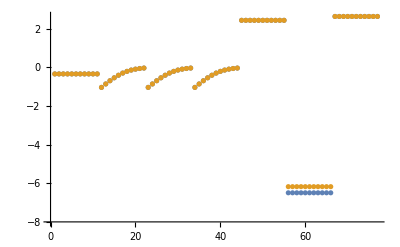

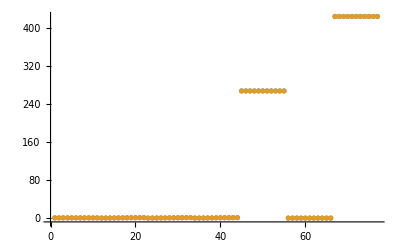

```mathematica
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[1,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[1,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution



```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```



```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```



```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```



```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=0.01;
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, absoluteRateForward, absoluteRateReverse, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

data value | predicted value | error in %
0.000045 | 0.000045 | 2.51272×10^-6
0.00089 | 0.00089 | 1.39821×10^-6
0.00053 | 0.00053 | 1.35758×10^-6

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.452 | 0.452 | 4.57492×10^-6